```mathematica
a0=1;Z=1;
```

```mathematica
NumPoints=100000;NumAtomicOrbitals=14;NumMolecularOrbitals=20;NumConfigurationOrbitals=50;
```

```mathematica
HydrogenWaveFunction[n_,l_,ml_][r_,θ_,ϕ_]:=√(((2Z)/(n a0))^3((n-l-1)!)/(2n((n+l)!)))E^(-Z/n r/a0)((2Z r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2Z r)/(n a0)]SphericalHarmonicY[l,ml,θ,ϕ]
```

```mathematica
STO3GG=<|"1s"->((2α)/π)^(3/4)E^(-α r^2),"2p"->((128 α^5)/π^3)^(1/4)x E^(-α r^2)|>;
```

```mathematica
StandardMolecularExponents=<|"H"-><|"K"->1.24|>,"C"-><|"K"->5.67,"L"->1.72|>,"N"-><|"K"->6.67,"L"->1.95|>,"O"-><|"K"->7.66,"L"->2.25|>|>;
```

```mathematica
STO3Gd=<|"K"->{0.44463454,0.53532814,0.15432897},"L"->{{0.70011547,0.39951283,-0.09996723},{0.39195739,0.60768372,0.15591627}}|>;
```

```mathematica
STO3Gα=<|"K"->{0.109818,0.405771,2.22766},"L"->{0.0751386,0.231031,0.994203}|>;
```

```mathematica
STO3GWaveFunctions[what_]:=<|"1s"->∑_(i=1)^3 (STO3Gd["K"][[i]]STO3GG["1s"]/.α->(STO3Gα["K"][[i]]*(StandardMolecularExponents[what]["K"])^2)),"2s"->∑_(i=1)^3 (STO3Gd["L"][[1]][[i]]STO3GG["1s"]/.α->(STO3Gα["L"][[i]]*(StandardMolecularExponents[what]["K"])^2)),"2p"->∑_(i=1)^3 (STO3Gd["L"][[2]][[i]]STO3GG["2p"]/.α->(STO3Gα["L"][[i]]*(StandardMolecularExponents[what]["K"])^2))|>
```

```mathematica
STO3GWaveFunctions["H"]["2p"]
```

0.377772 ⅇ^(-1.52869 r^2) x+0.237553 ⅇ^(-0.355233 r^2) x+0.0376324 ⅇ^(-0.115533 r^2) x

```mathematica
Evaluate[HydrogenOrbitals[r,0,0]]
```

{ⅇ^-r/(√π),(ⅇ^(-r/2) (2-r))/(4 √(2 π)),(ⅇ^(-r/2) r)/(4 √(2 π)),0,0,(ⅇ^(-r/3) (27-18 r+2 r^2))/(81 √(3 π)),(ⅇ^(-r/3) (4-(2 r)/3) r)/(27 √(2 π)),0,0,1/81 ⅇ^(-r/3) √(2/(3 π)) r^2,0,0,0,0}

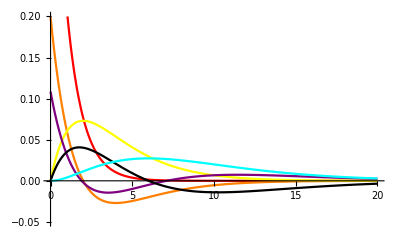

```mathematica
Plot[Evaluate[HydrogenOrbitals[r,.1,.1]],{r,0,20},PlotRange->{-0.05,0.2},PlotStyle->{Red,Orange,Yellow,Green,Blue,Purple,Black,Gray,Pink,Cyan}]
```

```mathematica
Reduce[D[HydrogenOrbitals[r,θ,ϕ][[3]],r]==0,r]
```

r==2||Cos[θ]==0

```mathematica
Reduce[HydrogenOrbitals[r,θ,ϕ][[3]]==0,r]
```

r==0||Cos[θ]==0

```mathematica
Abs[HydrogenOrbitals[r,θ,ϕ][[3]]]
```

(ⅇ^(-Re[r]/2) Abs[r Cos[θ]])/(4 √(2 π))

```mathematica
Contours->Function[{min,max},Range[min,max,0.01]]
```

```mathematica
Manipulate[Column[{ContourPlot[HydrogenOrbitals[√(x^2+y^2),ArcTan[y/x],0][[i]],{x,-10,10},{y,-10,10},Contours->Range[-0.2,0.2,.01],PlotRange->All,PlotLegends->True],IndexQuantumNumberMap[[i]]}],{i,Range[1,14]}]
```

```mathematica
ContourPlot3D[HydrogenOrbitals[{√(x^2+y^2+z^2),ArcTan[z,√(x^2+y^2+.0001)],ArcTan[x,y]}][[3]],{x,-10,10},{y,-10,10},{z,-10,10}]
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

$Aborted

```mathematica
Plot3D[Re[],{θ}]
```

```mathematica
SphericalPlot3D[]
```

```mathematica
(∫_0^(2π) ⅆϕ)(∫_0^π Sin[θ](∫_0^∞ (r^2 STO3GWaveFunctions["H"]["1s"]/.x->r Cos[θ])^2 ⅆr)ⅆθ)
```

1.94857

```mathematica
IndexQuantumNumberMap={{1,0,0},{2,0,0},{2,1,0},{2,1,1},{2,1,-1},{3,0,0},{3,1,0},{3,1,1},{3,1,-1},{3,2,0},{3,2,1},{3,2,-1},{3,2,2},{3,2,-2}};
```

```mathematica
HydrogenOrbitals[r_,θ_,ϕ_]=Table[(HydrogenWaveFunction@@IndexQuantumNumberMap[[i]])[r,θ,ϕ],{i,1,14}];
```

```mathematica
LCAO=Table[RandomPoint[Sphere[NumAtomicOrbitals]],{i,1,NumMolecularOrbitals}];
```

```mathematica
CONFIG=Table[RandomPoint[Sphere[NumMolecularOrbitals]],{i,1,NumConfigurationOrbitals}];
```

```mathematica
CoordinateTransform["Cartesian"->"Spherical",{x,y,z}]
```

{√(x^2+y^2+z^2),ArcTan[z,√(x^2+y^2)],ArcTan[x,y]}

```mathematica
Timing[Table[CONFIG.LCAO.(HydrogenOrbitals@@RandomPoint[Cuboid[{-1,-1,-1},{1,1,1}]]),{i,0,NumPoints}];]
```

{88.7209,Null}

```mathematica
Timing[Table[(CONFIG[[1]]).LCAO.(HydrogenOrbitals@@RandomPoint[Cuboid[{-1,-1,-1},{1,1,1}]]),{i,0,NumPoints}];]
```

{82.544,Null}